```mathematica
(***********************************************
Code corresponing to the publication
"New insights into mRNA trafficking in axons"
LF Gumy,EA Katrukha,LC Kapitein,CC Hoogenraad-Developmental neurobiology,2014

Part 2: Stochastic Monte-Carlo approach

email katpyxa@gmail.com for any questions
GNU General Public License
********************)

(* MAIN PARAMETERS *)
(* NB: time and space scale are dimensionless!*)
(* recalculate p value accordingly to get right scales*)

(* number of time steps *)
NSteps=200;
(* number of particles *)
nParticles=10;
(* probability of moving to the right *)
p=0.55;
(*Initial particles position *)
xini=0;

(* calculate trajectories *)
track=Table[0,{j,1,nParticles},{i,1,NSteps}];
For[i=2,i≤NSteps,i++,
For[j=1,j≤nParticles,j++,
val=Random[];
If[val≥p,
track[[j]][[i]]=track[[j]][[i-1]]+1;,
(*Unpermeable border on the left*)
If[track[[j]][[i-1]]==0,,track[[j]][[i]]=track[[j]][[i-1]]-1];
(**)
];
];
];
Print ["Done."];
```

Done.

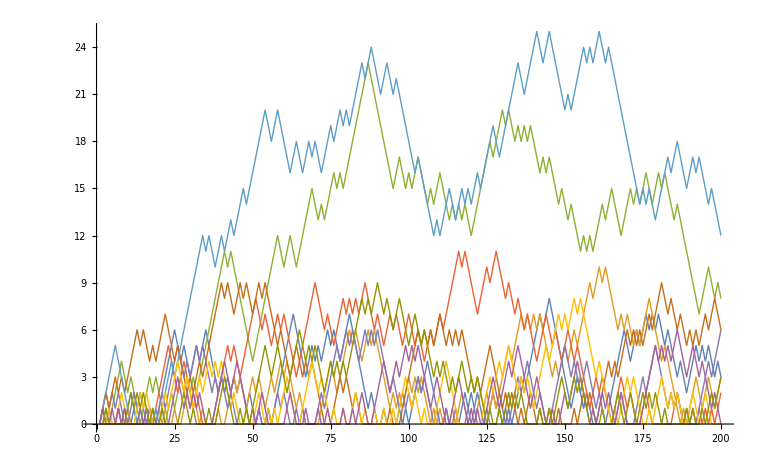

```mathematica
(* now let's visualize as a plot *)
ListPlot[track,Joined->True, PlotStyle->Thick]
```

```mathematica
(* animate particles movement *)
MovieAnimat={};
For[i=1,i≤NSteps,i++,
(*PointArray=Table[{PointSize[0.05],Hue[nParticles/j],Point[{track[[j]][[i]],0}]},{j,1,nParticles}];
MovieAnimat=Join[MovieAnimat,{Graphics[{PointSize[0.05],Hue[1],Point[{track[[1]][[i]],0}],Black,Dashed,Line[{{Min[track[[1]]]-1,0},{Max[track[[1]]]+1,0}}]}]}];*)
zz=Table[Hue[N[j/nParticles],1,1,0.5],{j,1,nParticles}];
(*zz=Hue[1];*)
MovieAnimat=Join[MovieAnimat,{Graphics[{PointSize[0.05],Point[Table[{track[[j]][[i]],0},{j,1,nParticles}],VertexColors->zz],Line[{{Min[track]-1,0},{Max[track]+1,0}}],Inset[Style[StringJoin["Steps N=",IntegerString[i]], Larger],{1.5,-4.6}]}]}];
];
ListAnimate[MovieAnimat,AnimationRunning->False]
```

```mathematica
(* export animation as avi movie *)
SetDirectory["C:\\Users\\Eugene\\Desktop"];
Export["multiple_partice_diffusion.avi",MovieAnimat,"FrameRate"->10]
```

multiple_partice_diffusion.avi